# FQ and MA in STIRAP

Show the different FQ and MA protocols in STIRAP. Which protocol offers the best control?

## Parameters and definitions

```mathematica
ℏ = 1
ti = 0
Δ= 0.1
(*Boundary conditions for the protocols*)
Ωpi = 0.1
Ωpf = 10
(*Range of the protocol time*)
Tmin = 0.1
Tmax = 50
(*Sample size*)
m = 9
ΔT = (Tmax-Tmin)/m
(*Protocols*)
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
(*Initial conditions - |n0 >*)
c10 = Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]
c20 = 0
c30 = -Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]
(*Initial conditions - |n- >*)
(*ϕ = 0.5*ArcTan[Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]/Δ]
c10 = (Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ]
c20 = -Sin[ϕ]
c30 = (Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ]*)
(*Counterdiabatic driving for the linear protocol*)
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
(*Energetic costs*)
Cost[Ωp_,Ωs_,Ωa_,Δ_,tf_] := NIntegrate[√(Δ^2 ℏ^2+(Ωa^2 ℏ^2)/2+(Ωp^2 ℏ^2)/2+(Ωs^2 ℏ^2)/2),{t,ti,tf}]/tf
Wex[c1_,c2_,c3_,Ωp_,Ωs_,Δ_] := ℏ*(Ωp*Re[c1*Conjugate[c2]] + Ωs*Re[c2*Conjugate[c3]]+ 2*Δ*Abs[c2]^2)
(*Sample points*)
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

1

0

0.1

0.1

10

0.1

50

9

5.54444

0.995037

0

-0.0995037

{0.0454959,2.56799,5.09049,7.61298,10.1355,12.658,15.1805,17.703,20.2255,22.748}

## Linear protocol

The linear protocol and the variation of the eigenvalues

1.

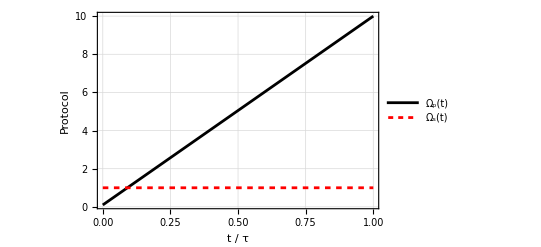

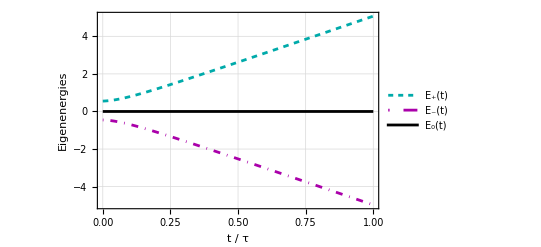

-Graphics-

```mathematica
tf = 1.0
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Cyan], Dashing[0.01]},FrameLabel ->{"t / τ", "Eigenenergies"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Left,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Magenta], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Left,0.78}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Black],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
```

## Minimal action

The protocols of the minimal action (MA) method comes from the minimization of the adiabatic action.

```mathematica
(*transitions between |n0 > and |n- > *)
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*transitions between |n0 > and |n+ >*)
ProtMA2 = Table[NDSolve[{D[ΩpMA2'[t]/(ΩpMA2[t]^2 + Ωs[t]^2),t] - 4*Δ/(ΩpMA2[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA2''[t] - 2.5*ΩpMA2[t]*ΩpMA2'[t]^2/(ΩpMA2[t]^2 + Ωs[t]^2)) ==0 , ΩpMA2[ti]==Ωpi, ΩpMA2[tf]==Ωpf},ΩpMA2,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*transitions between |n- > to |n+ >*)
(*ProtMA3 = Table[NDSolve[{D[ΩpMA3'[t]/(ΩpMA3[t]^2 + Ωs[t]^2),t] ==0 , ΩpMA3[ti]==Ωpi, ΩpMA3[tf]==Ωpf},ΩpMA3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]*)
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

{{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}},{{ΩpMA2→InterpolatingFunction[…]}}}

5

22.2778

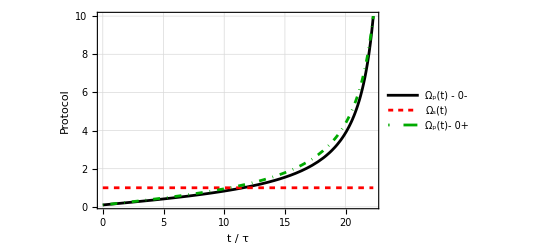

```mathematica
(*Protocol time for the Figure*)
n = 5
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - 0-",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]],Plot[Evaluate[ΩpMA2[t]/.Flatten[Part[ProtMA2, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green], DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)- 0+",10]},LegendLayout->"Row"],{Left,0.86}]](*,Plot[Evaluate[ΩpMA3[t]/.Flatten[Part[ProtMA3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Yellow], DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)- -+",10]},LegendLayout->"Row"],{Left,0.78}]]*)]
```

Solution of the Schrödinger equation for a system under the physical unitary transformation method.

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==c10,c2MA[ti]==c20,c3MA[ti]==c30 },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolMA2 = Table[NDSolve[{ⅈ*ℏ*c1MA2'[t] ==(ℏ/2)*Evaluate[ΩpMA2[t]/.Flatten[Part[ProtMA2,(tf-Tmin)/ΔT + 1]]]*c2MA2[t],ⅈ*ℏ*c2MA2'[t] ==(ℏ/2)*Evaluate[ΩpMA2[t]/.Flatten[Part[ProtMA2,(tf-Tmin)/ΔT + 1]]]*c1MA2[t]+(ℏ)*Δ*c2MA2[t]+ (ℏ/2)*Ωs[t]*c3MA2[t],ⅈ*ℏ*c3MA2'[t] ==+(ℏ/2)*Ωs[t]*c2MA2[t],c1MA2[ti]==c10,c2MA2[ti]==c20,c3MA2[ti]==c30 },{c1MA2,c2MA2,c3MA2},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

{{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}},{{c1MA2→InterpolatingFunction[…],c2MA2→InterpolatingFunction[…],c3MA2→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the minimal action protocol.

```mathematica
(*Population transfer*)
pMA1 = Table[Abs[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA2 = Table[Abs[c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA3 = Table[Abs[c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Population transfer 2*)
pMA12 = Table[Abs[c1MA2[t]/.Part[Flatten[Part[SolMA2,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA22 = Table[Abs[c2MA2[t]/.Part[Flatten[Part[SolMA2,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA32 = Table[Abs[c3MA2[t]/.Part[Flatten[Part[SolMA2,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexMA = Table[Wex[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexMAtimeaveraged= Table[NIntegrate[Wex[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1],c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2],c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CMA = Table[Cost[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.984324,0.00268822,0.0129772,0.0129414,0.0119442,0.0121853,0.0121445,0.0100712,0.00652405,0.00420834}

{0.0056101,0.200304,0.0163458,0.00139813,0.00601259,0.00833372,0.0057602,0.00185471,0.0000365165,0.000717096}

{0.0100656,0.797008,0.970677,0.98566,0.982043,0.979481,0.982095,0.988074,0.993439,0.995074}

{0.982805,0.0941014,0.00862959,0.00262613,0.00430399,0.00775481,0.0116661,0.0154003,0.0185162,0.0207095}

{0.00710345,0.198714,0.0710063,0.0306334,0.0159524,0.00919932,0.00555205,0.00337717,0.00200728,0.0011274}

{0.0100915,0.707186,0.920364,0.96674,0.979743,0.983045,0.982781,0.981222,0.979476,0.978163}

{-0.000498798,-0.26424,-0.109414,-0.0568212,-0.0307903,-0.0148949,-0.00603933,-0.00235867,-0.00177085,-0.00236481}

{-6.51827×10^-6,-0.0291714,-0.0121943,-0.00514598,-0.00277181,-0.0017463,-0.00121879,-0.000908907,-0.000705625,-0.00056105}

{1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the minimal action protocol.

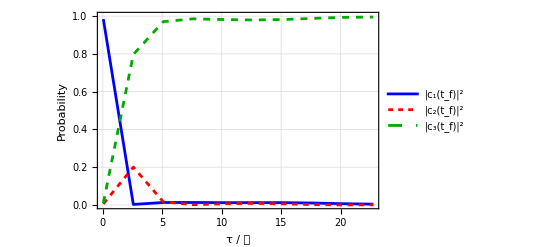

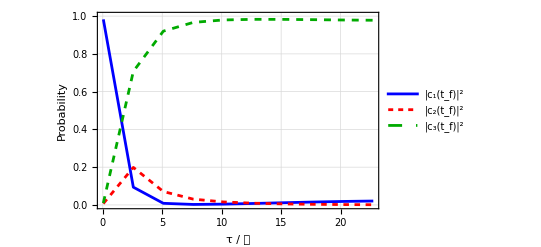

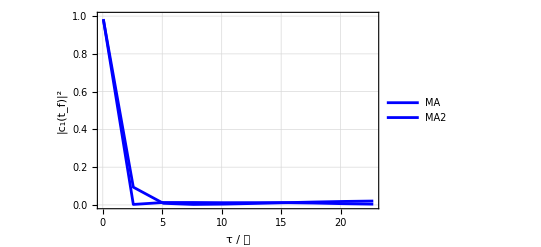

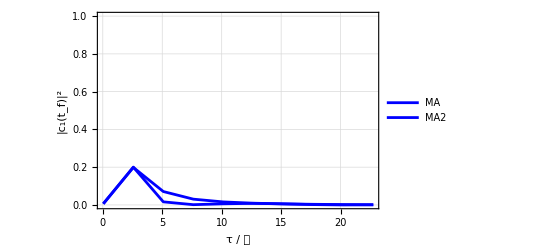

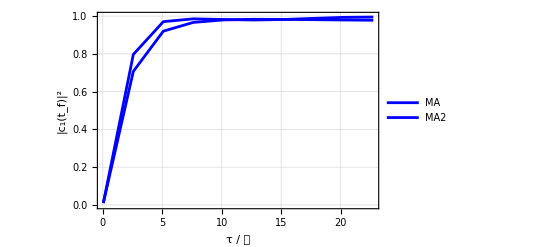

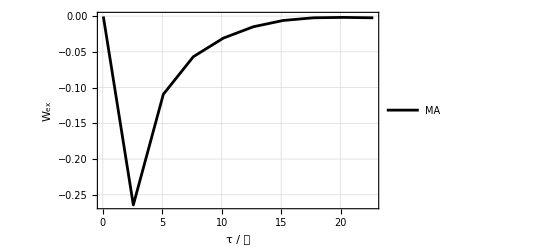

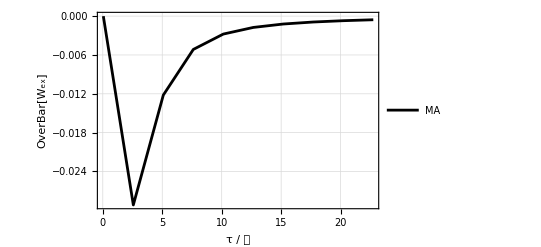

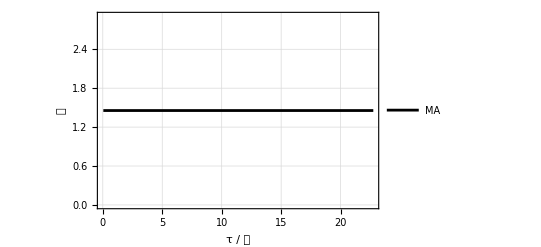

```mathematica
(*Population transfer*)
gMA = Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pMA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
gMA2 = Show[ListPlot[Transpose[{time,pMA12}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA22}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pMA32}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*MA Vs. MA2*)
Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_1(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA12}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pMA2}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_1(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA22}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pMA3}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "|c_1(t_f)|^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA32}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA2",10]},LegendLayout->"Row"],{Right,0.86}]]]
(*Excess work*)
 gWexMA = ListPlot[Transpose[{time,WexMA}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time-averaged excess work*)
 gWexMAtimeaveraged = ListPlot[Transpose[{time,WexMAtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCMA = ListPlot[Transpose[{time,CMA}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]]
```

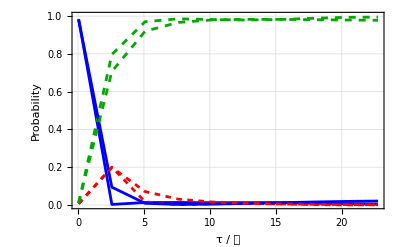

```mathematica
Show[gMA,gMA2]
```

## Fast quasidiabatic

The protocols for the fast quasidiabatic method (FQ) can be found by solving the EDO generated when we make the adiabatic quantitative condition constant.

```mathematica
(*Transitions between |n0 > and |n- >*)
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*Transitions between |n0 > and |n+ >*)
ProtFQ2 = Table[NDSolve[{D[ΩpFQ2'[t]/(ΩpFQ2[t]^2 + Ωs[t]^2)^(3/2)*(1-1.5*Δ/(ΩpFQ2[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ2[ti]==Ωpi, ΩpFQ2[tf]==Ωpf},ΩpFQ2,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*Transitions between |n- > and |n+ >*)
(*ProtFQ3 = Table[DSolve[{D[ΩpFQ3[t]*ΩpFQ3'[t]/(ΩpFQ3[t]^2 + Ωs[t]^2)^(4/2),t] ==0 , ΩpFQ3[ti]==Ωpi, ΩpFQ3[tf]==Ωpf},ΩpFQ3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]*)
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

{{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}}}

Protocols for the fast quasidiabatic method.

1

0.1

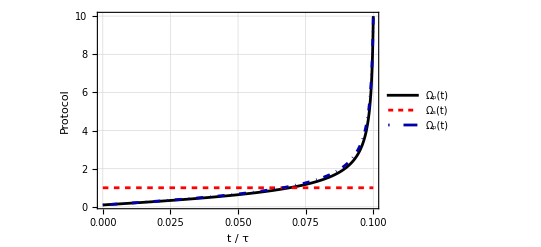

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]],Plot[Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Blue],DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.86}]](*,Plot[Evaluate[ΩpFQ3[t]/.Flatten[Part[ProtFQ3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green],Dashing[0.01]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.78}]]*)]
```

Solution of the Schrödinger equation for the fast quasidiabatic protocol.

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==c10,c2FQ[ti]==c20,c3FQ[ti]==c30 },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolFQ2 = Table[NDSolve[{ⅈ*ℏ*c1FQ2'[t] ==(ℏ/2)*Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2,(tf-Tmin)/ΔT + 1]]]*c2FQ2[t],ⅈ*ℏ*c2FQ2'[t] ==(ℏ/2)*Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2,(tf-Tmin)/ΔT + 1]]]*c1FQ2[t]+(ℏ)*Δ*c2FQ2[t]+ (ℏ/2)*Ωs[t]*c3FQ2[t],ⅈ*ℏ*c3FQ2'[t] ==+(ℏ/2)*Ωs[t]*c2FQ2[t],c1FQ2[ti]==c10,c2FQ2[ti]==c20,c3FQ2[ti]==c30 },{c1FQ2,c2FQ2,c3FQ2},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

{{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}},{{c1FQ2→InterpolatingFunction[…],c2FQ2→InterpolatingFunction[…],c3FQ2→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

```mathematica
(*Population transfer*)
pFQ1 = Table[Abs[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ2 = Table[Abs[c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ3 = Table[Abs[c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ12 = Table[Abs[c1FQ2[t]/.Part[Flatten[Part[SolFQ2,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ22 = Table[Abs[c2FQ2[t]/.Part[Flatten[Part[SolFQ2,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ32 = Table[Abs[c3FQ2[t]/.Part[Flatten[Part[SolFQ2,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexFQ = Table[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexFQtimeaveraged= Table[NIntegrate[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1],c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2],c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CFQ = Table[Cost[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.988126,0.0359962,0.0447439,0.0106516,0.00961527,0.0153444,0.00834906,0.0151417,0.00773029,0.00860836}

{0.00187438,0.146895,0.0654347,0.00742654,0.0125174,0.00648906,0.00659016,0.00280291,0.000953244,0.00489469}

{0.00999996,0.817108,0.889821,0.981922,0.977867,0.978166,0.985061,0.982055,0.991316,0.986497}

{0.987821,0.0594604,0.0327349,0.0200149,0.00867677,0.0123507,0.0102846,0.0133282,0.0122048,0.0052497}

{0.00217101,0.0851057,0.0710287,0.00443193,0.00598258,0.00892775,0.00287533,0.00379872,0.00128544,0.00113517}

{0.0100075,0.855433,0.896236,0.975553,0.985341,0.978721,0.98684,0.982873,0.98651,0.993615}

{-0.000602043,-0.3779,0.0504174,0.0117853,-0.0678195,0.0281024,0.000198183,-0.0220817,0.00970121,-0.00200368}

{-3.36497×10^-6,-0.0122677,-0.000760596,-0.00230784,-0.000591812,-0.000279874,-0.000517296,-0.000201298,-0.000156836,-0.000183686}

{1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

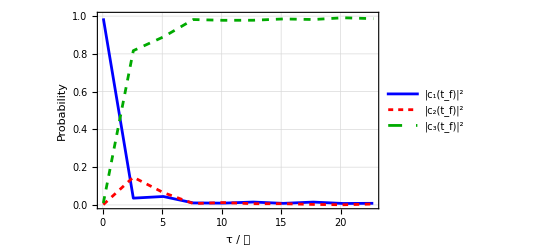

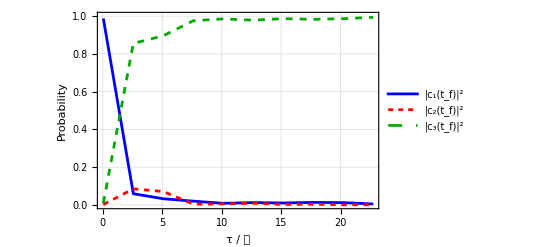

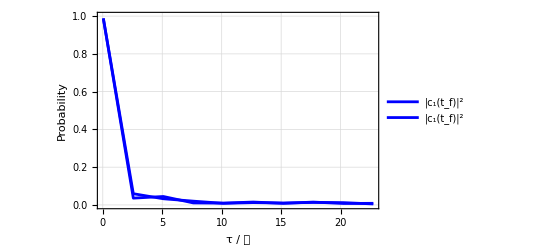

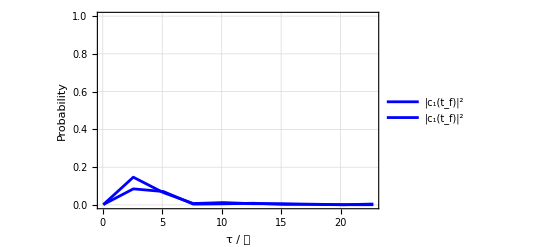

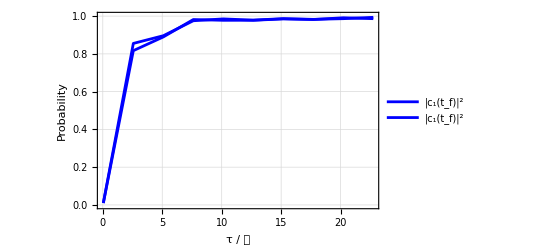

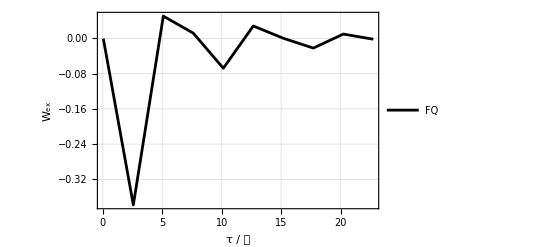

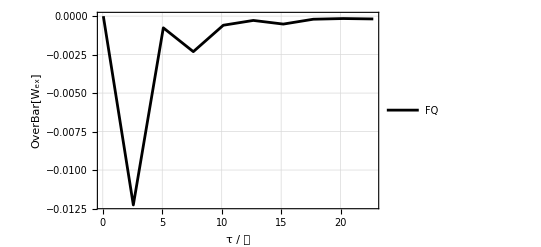

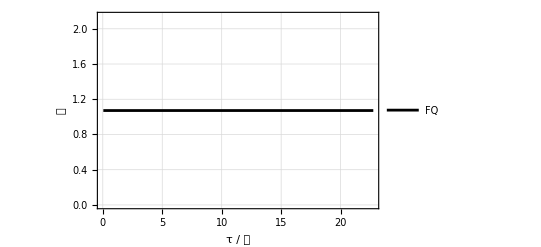

```mathematica
(*Population transfer*)
gFQ = Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pFQ2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pFQ3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
gFQ2 = Show[ListPlot[Transpose[{time,pFQ12}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pFQ22}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pFQ32}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]], 
ListPlot[Transpose[{time,pFQ12}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pFQ2}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]], 
ListPlot[Transpose[{time,pFQ22}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[ListPlot[Transpose[{time,pFQ3}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]], 
ListPlot[Transpose[{time,pFQ32}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]]]
(*Excess work*)
 gWexFQ = ListPlot[Transpose[{time,WexFQ}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time-averaged excess work*)
 gWexFQtimeaveraged = ListPlot[Transpose[{time,WexFQtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCFQ = ListPlot[Transpose[{time,CFQ}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.94}]]
```

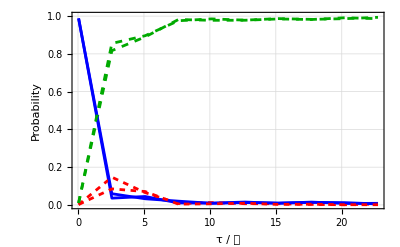

```mathematica
Show[gFQ,gFQ2]
```